Funkcja Fit

Fit[data, funs, vars]  stosuje aproksymacje kwadratowa  
data - punkty wejsciowe aproksymacji 
funs - funkcje bazowe
vars - lista argumentow funkcji bazowych.

Przyklad:

Tworzymy tabele liczb pierwszych

```mathematica
tableprimes=Table[Prime[x],{x,20}];
```

Pokazujemy je na wykresie

```mathematica
plotprimes=ListPlot[tableprimes,PlotStyle->PointSize[0.02]];
```

Aproksymujemy wartosci bazujac na wielomianach

```mathematica
qfit=Fit[tableprimes,{1,x,x^2},x];
```

Rysujemy wykres funkcji aproksymujacej:

```mathematica
plotfit=Plot[qfit,{x,0,20}];
```

Oto, jak wyglada porownanie funkcji aproksymujacej  z punktami wejsciowymi

```mathematica
Show[plotfit,plotprimes];
```

Zadanie 1
Narysowac wykres bledu aproksymacji z przykladu .

Zadanie 2 
Wymyslic funkcje inna niz Prime[x]. Zaproksymowac ja w taki sam sposob jak w przykladzie. UWAGA : ocena bedzie proporcjonalna do orginalnosci wymyslonej funkcji
tzn im wiecej osob bedzie mialo ta sama funkcje, tym gorsza ocena.
    
Zadanie 3
Przerobic przyklad tak, aby korzystal z funkcji PolinamialFit pakietu Numerical Math. Odpowiednie informacje znajduja sie w systemie pomocy dla "Add-Ons" , Standard Packages, NumericalMath.

Zadanie 4
Zapoznac sie z funkcja TrigFit.(System pomocy dla "Add-Ons" , Standard Packages, NumericalMath)
Co ona robi? Podac przyklad aproksymacji za pomoca funkcji trygonometrycznych . W przypadku jakich funkcji warto ja stosowac ?

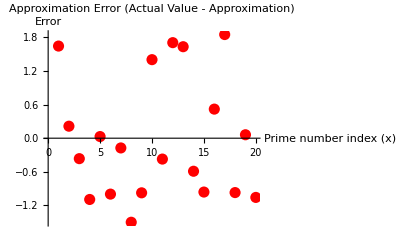

```mathematica
(*Zadanie 1: Wykres błędu aproksymacji*)tableprimes=Table[Prime[x],{x,20}];
qfit=Fit[tableprimes,{1,x,x^2},x];
errors=Table[{x,Prime[x]-(qfit/. x->i/. i->x)},{x,1,20}];
ListPlot[errors,PlotStyle->{PointSize[0.02],Red},PlotLabel->"Approximation Error (Actual Value - Approximation)",AxesLabel->{"Prime number index (x)","Error"}]
```

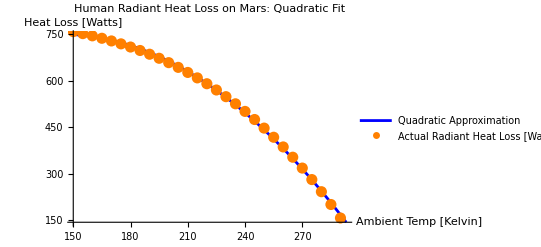

```mathematica
(*Zadanie 2: Aproksymacja własnej funkcji*)

(*At first i thought about the cooling of Earth`s surface at night and how i could calculate it, then on Mars and i found good explanation of how it works with almost no atmosphere*)

(*Radiant Heat Loss of a Human on Mars*)
(*Based on the Stefan-Boltzmann Law from the Quora post*)

(*https://en.wikipedia.org/wiki/Climate_of_Mars#Temperature*)
(*https://www.quora.com/What-is-the-temperature-at-the-Equator-of-Mars-and-what-is-the-lowest-temperature-the-following-area-can-drop-to*)

(*Constants:e=0.95,sigma=5.67*10^-8,A=1.7 m^2,T_skin=306.15 K (33 C)*)(*The function calculates Watts lost based on ambient temperature in Kelvin (Ta)*)heatLossFunc[Ta_]:=0.95*5.67*10^-8*1.7*(306.15^4-Ta^4)

(*Generate data points for Martian temperatures from 150K (-123 C) to 293K (20 C)*)
marsHeatData=Table[{Ta,heatLossFunc[Ta]},{Ta,150,293,5}];

plotMarsHeatData=ListPlot[marsHeatData,PlotStyle->{PointSize[0.02],Orange},PlotLegends->{"Actual Radiant Heat Loss [Watts]"}];

(*Approximate the T^4 radiation curve using a quadratic polynomial*)
quadraticFitHeat=Fit[marsHeatData,{1,Ta,Ta^2},Ta];

plotQuadraticFitHeat=Plot[quadraticFitHeat,{Ta,150,293},PlotStyle->Blue,PlotLegends->{"Quadratic Approximation"}];

Show[plotQuadraticFitHeat,plotMarsHeatData,PlotLabel->"Human Radiant Heat Loss on Mars: Quadratic Fit",AxesLabel->{"Ambient Temp [Kelvin]","Heat Loss [Watts]"}]
```

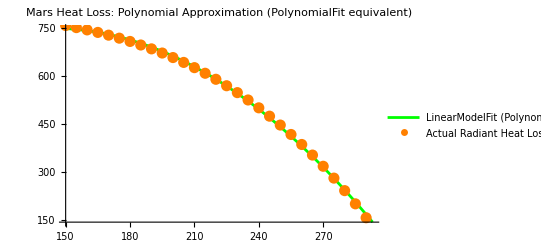

```mathematica
(*ZADANIE 3:Użycie (odpowiednika) PolynomialFit dla naszego modelu Marsa*)polyFitMarsModern=LinearModelFit[marsHeatData,{1,Ta,Ta^2},Ta];

plotPolyFitMarsModern=Plot[polyFitMarsModern[Ta],{Ta,150,293},PlotStyle->Green,PlotLegends->{"LinearModelFit (PolynomialFit)"}];

Show[plotPolyFitMarsModern,plotMarsHeatData,PlotLabel->"Mars Heat Loss: Polynomial Approximation (PolynomialFit equivalent)"]
```

```mathematica
Co robi funkcja TrigFit?
Funkcja TrigFit z dawnego pakietu NumericalMath(w nowoczesnej Mathematice jej funkcjonalność przejęły wbudowane funkcje takie jak Fit,LinearModelFitoraztransformatyFouriera)służyładowyznaczaniawielomianówtrygonometrycznychdopasowanychdozbiorudanychpunktowych.

W przypadku jakich funkcji warto ją stosować? Metodę tę warto stosować do analizy danych okresowych,czyli zjawisk, które powtarzają się w regularnych cyklach w czasie lub przestrzeni. 
Główne obszary zastosowań to:
Przetwarzanie sygnałów i akustyka: aproksymacja i analiza fal dźwiękowych
Meteorologia:modelowanierocznychlubdobowychwahańtemperatury,na słonecznienia czy pływów morskich.
Fizykaiinżynieria:analizadrgańmechanicznych,układówoscylującychorazprąduzmiennego.
```

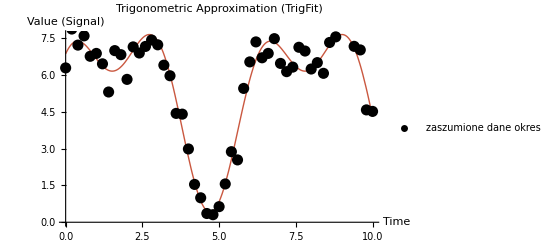

```mathematica
(*Zadanie 4:Funkcja TrigFit (Aproksymacja Trygonometryczna)*)
(*Generujemy zaszumione dane okresowe (np.wahania jakiegoś sygnału)*)trigData=Table[{x,5+3 Sin[x]+2 Cos[2 x]+RandomReal[{-1,1}]},{x,0,10,0.2}];
plotTrigData=ListPlot[trigData,PlotStyle->{PointSize[0.02],Black},PlotLegends->{"zaszumione dane okresowe"}];

(*Wykonujemy dopasowanie trygonometryczne (współczesny odpowiednik TrigFit) Jako bazę podajemy jedynkę oraz sinusy i cosinusy wielokrotności x*)
modernTrigFit=Fit[trigData,{1,Sin[x],Cos[x],Sin[2 x],Cos[2 x]},x];


plotModernTrigFit=Plot[modernTrigFit,{x,0,10},PlotStyle->Thick,ColorFunction->"Rainbow",PlotLegends->{"Trigonometric Approximation (TrigFit)"}];

Show[plotModernTrigFit,plotTrigData,PlotLabel->"Trigonometric Approximation (TrigFit)",AxesLabel->{"Time","Value (Signal)"}]
```